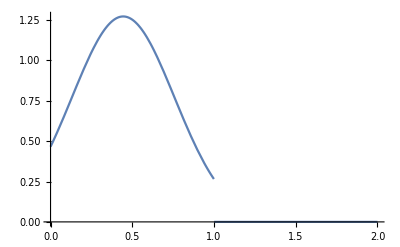

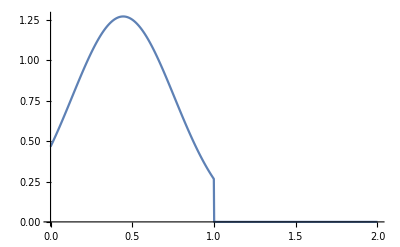

histvecth.csv

xvecth.csv

```mathematica
Clear["Global`*"];
(*Solving for the delta *)
r = 1.6;
sigma = 0.8;
start = (1-1/r)^2 +0.1;
sol = FindRoot[(ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √q (-1+r) r sigma-ⅇ^(-1/(2 q r^2 sigma^2)) √q r (-1+2 r) sigma-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q sigma)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r sigma)])/(√(2 π) r^2)+1/2 Erfc[1/(√2 √q r sigma)]==q,{q, start}];

q0 = q/.sol;

f[x_]:= 1/Sqrt[2Pi q0 sigma^2] Exp[-(x-(1-1/r))^2/(2sigma^2q0)]HeavisideTheta[1-x] ;


Plot[f[x], {x, 0,2}]
xmin = 0;
xmax = 2;
numx = 1000;
xvec = Table[x,{x,xmin,xmax,(xmax-xmin)/(numx-1)}];
histvec = f[xvec];
ListLinePlot[Transpose[{xvec,histvec}],PlotRange->All]

SetDirectory[NotebookDirectory[]];
Export["histvecth.csv",N[histvec]]
Export["xvecth.csv",N[xvec]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in myx near {myx} = {0.0644376}. NIntegrate obtained 357.925 and 299.396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in myx near {myx} = {0.0644376}. NIntegrate obtained 30.6777 and 0.550557 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in myx near {myx} = {0.0644376}. NIntegrate obtained 15.6607 and 0.00771323 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

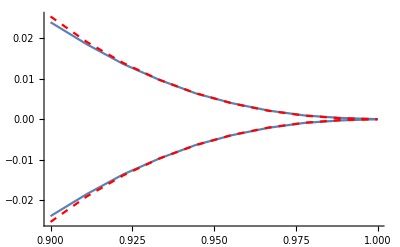

xvecjaccutoff_test.csv

yvecjaccutoff_test.csv

yvecjaccutoff_approx_test.csv

```mathematica
Clear["Global`*"];

r =1.6;
sigma =0.8;
start = (1-1/r)^2+0.1;
sol = FindRoot[(ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √q (-1+r) r sigma-ⅇ^(-1/(2 q r^2 sigma^2)) √q r (-1+2 r) sigma-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q sigma)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r sigma)])/(√(2 π) r^2)+1/2 Erfc[1/(√2 √q r sigma)]==q,{q, start}];

q0 = q/.sol;



xmin = 0.9;
xmax =0.9999;
numx = 10;
xvec = Table[s, {s, xmin, xmax, (xmax-xmin)/(numx-1)}];
crityvec = Table[s,{s, xmin, xmax, (xmax-xmin)/(numx-1)}];
crityvecapprox = Table[s,{s, xmin, xmax, (xmax-xmin)/(numx-1)}];
numy = 100;
ymin = 0; 
ymax =0.03;
yvec = Table[y,{y,ymin, ymax, (ymax - ymin)/(numy -1)}];





effinf  =1000;
eps = 0.0000001;
phi1 =(√q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2));
Monitor[For[j= 1, j<numx+1, j++,
x = xvec[[j]];
fvec = Table[y,{y,ymin, ymax, (ymax - ymin)/(numy -1)}];
fvecapprox = Table[y,{y,ymin, ymax, (ymax - ymin)/(numy -1)}];
For[i = 1, i<numy+1, i++,
y = yvec[[i]];

start =10.0;



fvec[[i]] = NIntegrate[sigma^2 Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] r^2myx^2/((1 - r myx - x)^2+y^2),{myx, 0, 1}];(* +  phi1 r^2sigma^2/((1 - r - x)^2+y^2);*)


];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
crityvec[[j]] = yvec[[pos]];
];,j];
px[x_]:=Exp[-(x-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0];

(*wyapprox[wx_]:=wy/.FindRoot[px[(1-wx)/r] (sigma^2 (r wy+((1-wx)^2) Pi/2+((1-wx)^2) Pi/2+(-1+wx) wy Log[(1-wx)^2]+wy(1-wx ) Log[r^2]))/(r wy)==1,{wy,0.01}];*)
(*wyapprox[wx_]:= wy/.FindRoot[phi sigma^2+ px[(1-wx)/r] (sigma^2 ((-1+wx) (-1+wx) Pi/2+(-1+wx) (-1+wx) Pi/2+(-1+wx) wy Log[1-2 wx+wx^2]+(wy-wx wy) Log[r^2]))/(r wy)==1,{wy,0.01}]*)

(*crityvecapprox = Table[( Pi (1-x)^2 - (1-x )(( Pi (1-x)^2)(1/(sigma^2 px[(1-x)/r])-1)/r)Log[(1-x)^2/r^2])(1/(sigma^2 px[(1-x)/r])-1)/r,{x, xmin, xmax, (xmax-xmin)/(numx-1)}];*)
(*wyapprox[wx_]:=(π sigma^2 (-1+wx)^2 px[(1-wx)/r])/(r-sigma^2 (r-2(1-wx) Log[(1-wx)/r]) px[(1-wx)/r]);*)
phi = (√q0 sigma (-Erf[(-1+1/r)/(√2 √q0 sigma)]+Erf[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2));
wyapprox[wx_]:=(π sigma^2 (-1+wx)^2 px[(1-wx)/r])/(r-phi r sigma^2+sigma^2 (-1+wx) (Log[r^2]-Log[(-1+wx)^2]) px[(1-wx)/r]);
(*wyapprox[wx_]:=(π sigma^2 (-1+wx)^2 px[(1-wx)/r])/(r-phi r sigma^2);*)
crityvecapprox = Table[wyapprox[x],{x, xmin, xmax, (xmax-xmin)/(numx-1)}];

plt1 = ListLinePlot[Transpose[{ xvec,crityvec}], PlotRange->All];
plt2 = ListLinePlot[Transpose[{ xvec,-crityvec}], PlotRange->All];
plt3= ListLinePlot[Transpose[{ xvec,crityvecapprox}], PlotRange->All, PlotStyle->{Red,Dashed}];
plt4= ListLinePlot[Transpose[{ xvec,-crityvecapprox}], PlotRange->All, PlotStyle->{Red,Dashed}];
Show[plt2, plt1,plt3, plt4, PlotRange->All]



SetDirectory[NotebookDirectory[]];
Export["xvecjaccutoff_test.csv", xvec]
Export["yvecjaccutoff_test.csv", crityvec]
Export["yvecjaccutoff_approx_test.csv", crityvecapprox]
```

```mathematica
Export["xvecjaccutoffsig0point5r1point9.csv", xvec]
Export["yvecjaccutoffsig0point5r1point9.csv", crityvec]
```

xvecjaccutoffsig0point5r1point9.csv

yvecjaccutoffsig0point5r1point9.csv

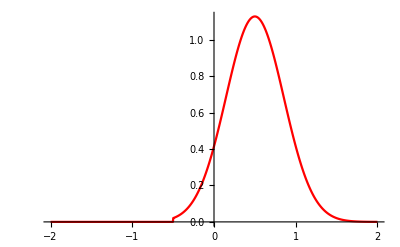

diaghistvecth.csv

diagxvecth.csv

```mathematica
Clear["Global`*"];

r = 1.5;
sigma = Sqrt[0.3];
start = (1-1/r)^2;
sol = FindRoot[(-ⅇ^(-(-1+1/r)^2/(2 q)) √q (-1+r) r (-2+sigma) sigma-ⅇ^(-1/(2 q r^2)) √q r sigma (-2+2 r+sigma)-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r)])/(√(2 π) r^2)+1/2 Erfc[1/(√2 √q r)]==q,{q, start}];

q0 = q/.sol;

px[x_]:= 1/Sqrt[2Pi sigma^2r^2q0] Exp[-(x-2+r)^2/(2 sigma^2 r^2q0)]HeavisideTheta[x-(1-r)] ;

plt1  = Plot[px[x_], {x, -2,2}];


xmin = -2;
xmax = 2;
numx = 1000;
xvec = Table[x,{x,xmin,xmax,(xmax-xmin)/(numx-1)}];
histvec = px[xvec];
plt2 =ListLinePlot[Transpose[{xvec,histvec}],PlotRange->All, PlotStyle->Red];
Show[plt1,plt2]

SetDirectory[NotebookDirectory[]];
Export["diaghistvecth.csv",N[histvec]]
Export["diagxvecth.csv",N[xvec]]
```

```mathematica
NIntegrate[px[x], {x,-Infinity, Infinity}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.497111}. NIntegrate obtained 0.997666 and 6.09883×10^-6 for the integral and error estimates.

0.997666

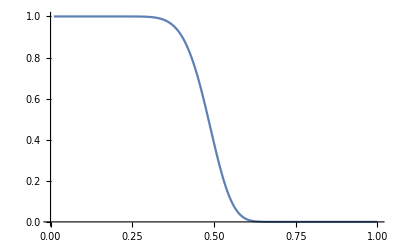

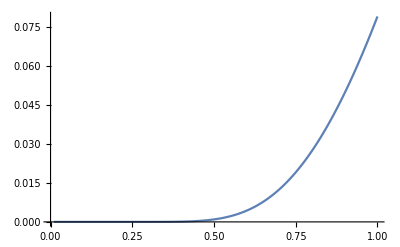

```mathematica
Clear["Global`*"];

gamma = 0;
mu = 0;
r = 1.5;
myn = 1000;

sigmamin = 0.1;
sigmamax =1.0;
numsigma= 1000;
sigmavec = Table[s, {s, sigmamin, sigmamax, (sigmamax-sigmamin)/(numsigma-1)}];
probvec = Table[s, {s, sigmamin, sigmamax, (sigmamax-sigmamin)/(numsigma-1)}];
fvec = Table[s, {s, sigmamin, sigmamax, (sigmamax-sigmamin)/(numsigma-1)}];




w0funct[mydelta_] := 0.5(1.0 + Erf[mydelta/Sqrt[2.0]]);
w1funct[mydelta_] := 0.5 (Sqrt[2.0/Pi]Exp[-mydelta^2/2.0]+ mydelta (1.0 + Erf[mydelta/Sqrt[2]]));
w2funct[mydelta_] := w0funct[mydelta] + mydelta w1funct[mydelta];


effinf  =1000;
eps = 0.0000001;
Monitor[For[j= 1, j<numsigma+1, j++,
sigma = sigmavec[[j]];


start =10.0;

(*Solving for the delta *)
sol = FindRoot[{sigma^2 ((1+gamma)( 0.5(1.0 + Erf[mydelta/Sqrt[2.0]])) + mydelta ( 0.5 (Sqrt[2.0/Pi]Exp[-mydelta^2/2.0]+ mydelta (1.0 + Erf[mydelta/Sqrt[2]]))))^2==( ( 0.5(1.0 + Erf[mydelta/Sqrt[2.0]])) + mydelta ( 0.5 (Sqrt[2.0/Pi]Exp[-mydelta^2/2.0]+ mydelta (1.0 + Erf[mydelta/Sqrt[2]]))))},{mydelta, start}];
{delta} = {mydelta} /.sol;
w0 = 0.5(1.0 + Erf[delta/Sqrt[2.0]]);
w1 = 0.5 (Sqrt[2.0/Pi]Exp[-delta^2/2.0]+ delta (1.0 + Erf[delta/Sqrt[2]]));
w2 = w0 + delta w1;

(*Phi is indepenent of mu*)
phi = w0;


(*Finds the fixed-point quantities*)
chi0 = w0 + gamma w0^2/w2;
m0 = (delta/w1 w2/(w2 + gamma w0)-mu)^(-1)*(1-1/r);
b = w2/(w2 + gamma w0);
q0 = (b m0 /(sigma w1))^2;

myf = 1/2 (1+Erf[(-3+r+m0 mu r)/(√2 √q0 r sigma)]);
probvec[[j]] = (1-myf)^myn;
fvec[[j]] = myf;

];,j];

plt1 = ListLinePlot[Transpose[{ sigmavec^2,probvec}], PlotRange->All]
plt1 = ListLinePlot[Transpose[{ sigmavec^2,fvec}], PlotRange->All]
(*SetDirectory[NotebookDirectory[]];
Export["sigmavec.csv",N[sigmavec]]
Export["probvecn1000.csv",N[probvec]]*)
```

```mathematica
Clear["Global`*"];Integrate[ Exp[-(myx-(1-1/r +mu m0))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0],{myx,2/r,Infinity }]
```

ConditionalExpression[(√q0 sigma (√q0 √(1/(q0 sigma^2)) sigma+Erf[(-3+r+m0 mu r)/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2)), ]

```mathematica
Simplify[(1+Erf[(-3+r+m0 mu r)/(√2 √q0 r sigma)])/2]
```

1/2 (1+Erf[(-3+r+m0 mu r)/(√2 √q0 r sigma)])

```mathematica
Clear["Global`*"];
Integrate[Exp[-z^2/2]/Sqrt[2Pi] (1-1/r + sigma Sqrt[q] z)^2, {z, (1/r-1)/(Sqrt[q]sigma), 1/(r sigma Sqrt[q])}] +Integrate[Exp[-z^2/2]/Sqrt[2Pi] , {z, 1/(r sigma Sqrt[q]), Infinity}]
```

(ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √q (-1+r) r sigma-ⅇ^(-1/(2 q r^2 sigma^2)) √q r (-1+2 r) sigma-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q sigma)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r sigma)])/(√(2 π) r^2)+1/2 Erfc[1/(√2 √q r sigma)]

```mathematica
Clear["Global`*"];
Integrate[ 1/Sqrt[2Pi q0 sigma^2] Exp[-(x-(1-1/r))^2/(2sigma^2q0)] ,{x, 1, Infinity}]
```

ConditionalExpression[(√q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2)), ]

```mathematica
Clear["Global`*"];
Solve[1 == r^2(1 - xi + etai)(1- r xi (1 - xi + etai)+ r xii), xi]
```

{{xi→(2 (r^3+etai r^3))/(3 r^3)-(2^(1/3) (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii))/(3 r^3 (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3))+1/(3 2^(1/3) r^3)(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3)},{xi→(2 (r^3+etai r^3))/(3 r^3)+((1+ⅈ √3) (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii))/(3 2^(2/3) r^3 (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3))-1/(6 2^(1/3) r^3)(1-ⅈ √3) (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3)},{xi→(2 (r^3+etai r^3))/(3 r^3)+((1-ⅈ √3) (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii))/(3 2^(2/3) r^3 (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3))-1/(6 2^(1/3) r^3)(1+ⅈ √3) (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3)}}

```mathematica
Simplify[(2 (r^3+etai r^3))/(3 r^3)-(2^(1/3) (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii))/(3 r^3 (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3))+1/(3 2^(1/3) r^3)(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii+√(4 (3 r^5-r^6-2 etai r^6-etai^2 r^6+3 r^6 xii)^3+(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+9 r^9 xii+9 etai r^9 xii)^2))^(1/3)]
```

1/(6 r^3)(4 (1+etai) r^3+(2 2^(1/3) r^5 (-3+r (1+2 etai+etai^2-3 xii)))/(-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+√(r^12 ((27-9 (1+etai) r^2+(1+etai) r^3 (2+4 etai+2 etai^2-9 xii))^2-4 r^3 (-3+r (1+2 etai+etai^2-3 xii))^3))+9 r^9 xii+9 etai r^9 xii)^(1/3)+2^(2/3) (-27 r^6+9 r^8+9 etai r^8-2 r^9-6 etai r^9-6 etai^2 r^9-2 etai^3 r^9+√(r^12 ((27-9 (1+etai) r^2+(1+etai) r^3 (2+4 etai+2 etai^2-9 xii))^2-4 r^3 (-3+r (1+2 etai+etai^2-3 xii))^3))+9 r^9 xii+9 etai r^9 xii)^(1/3))

```mathematica
Clear["Global`*"];
 Integrate[ myx^2 Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] ,{myx, 0, k}] +   Integrate[k^2  Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] ,{myx, k, Infinity}]
```

ConditionalExpression[(√q0 sigma ((2 ⅇ^(-(-1+1/r)^2/(2 q0 sigma^2)) √q0 (-1+r) sigma)/r-(2 ⅇ^(-(-1+k+1/r)^2/(2 q0 sigma^2)) √q0 (-1+r+k r) sigma)/r-(√(2 π) (-1+r)^2 Erf[(1-k-1/r)/(√2 √q0 sigma)])/r^2-√(2 π) q0 sigma^2 Erf[(-1+1/r)/(√2 √q0 sigma)]+√(2 π) q0 sigma^2 Erf[(-1+k+1/r)/(√2 √q0 sigma)]+(√(2 π) (-1+r)^2 Erf[(-1+r)/(√2 √q0 r sigma)])/r^2))/(2 √(2 π) √(q0 sigma^2))+(k^2 √q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[(1+(-1+k) r)/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2)), ]

```mathematica
Simplify[1/(2 √(2 π) √(q0 sigma^2))√q0 sigma ((2 ⅇ^(-(-1+1/r)^2/(2 q0 sigma^2)) √q0 (-1+r) sigma)/r-(2 ⅇ^(-(-1+k+1/r)^2/(2 q0 sigma^2)) √q0 (-1+r+k r) sigma)/r-(√(2 π) (-1+r)^2 Erf[(1-k-1/r)/(√2 √q0 sigma)])/r^2-√(2 π) q0 sigma^2 Erf[(-1+1/r)/(√2 √q0 sigma)]+√(2 π) q0 sigma^2 Erf[(-1+k+1/r)/(√2 √q0 sigma)]+(√(2 π) (-1+r)^2 Erf[(-1+r)/(√2 √q0 r sigma)])/r^2)+(k^2 √q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[(1+(-1+k) r)/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2))/.q0->q]
```

1/(2 √(q sigma^2))√q sigma ((ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √(2/π) √q (-1+r) sigma)/r-(ⅇ^(-(-1+k+1/r)^2/(2 q sigma^2)) √(2/π) √q (-1+r+k r) sigma)/r-((-1+r)^2 Erf[(1-k-1/r)/(√2 √q sigma)])/r^2-q sigma^2 Erf[(-1+1/r)/(√2 √q sigma)]+q sigma^2 Erf[(-1+k+1/r)/(√2 √q sigma)]+((-1+r)^2 Erf[(-1+r)/(√2 √q r sigma)])/r^2+k^2 (-1+√q √(1/(q sigma^2)) sigma+Erfc[(1+(-1+k) r)/(√2 √q r sigma)]))

```mathematica
Clear["Global`*"];
 Integrate[  Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] ,{myx, 0, 1}]
```

(√q0 sigma (-Erf[(-1+1/r)/(√2 √q0 sigma)]+Erf[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2))

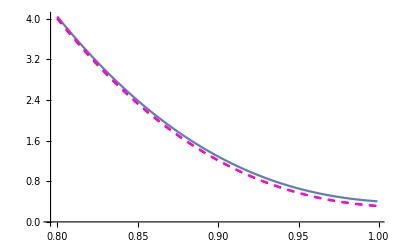

```mathematica
Clear["Global`*"];
r = 1.6;
sigma = 0.7;
start = (1-1/r)^2+0.1;
sol = FindRoot[(ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √q (-1+r) r sigma-ⅇ^(-1/(2 q r^2 sigma^2)) √q r (-1+2 r) sigma-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q sigma)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r sigma)])/(√(2 π) r^2)+1/2 Erfc[1/(√2 √q r sigma)]==q,{q, start}];

q0 = q/.sol;
myy = 0.01;

f[x_,y_]:=NIntegrate[sigma^2 Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] r^2myx^2/((1 - r myx - x)^2+y^2),{myx, 0, 1}];
px[x_]:=Exp[-(x-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0];
fapprox[wx_,wy_]:=px[(1-wx)/r] (sigma^2 (r wy-(-1+wx-wy) (-1+wx+wy) ArcTan[(-1+wx)/wy]+(-1+wx-wy) (-1+wx+wy) ArcTan[(-1+r+wx)/wy]+(-1+wx) wy Log[1-2 wx+wx^2+wy^2]+(wy-wx wy) Log[1+r^2+2 r (-1+wx)-2 wx+wx^2+wy^2]))/(r wy);(*px[(1-x)/r]Pi sigma^2 (1-x)^2/ r/0.05;*)
(*fapprox2[wx_,wy_]:=px[(1-wx)/r](sigma^2 (-1+wx)^2 (-ArcTan[(-1+wx)/wy]+ArcTan[(-1+r+wx)/wy]))/(r wy) ;*)
fapprox2[wx_,wy_]:=px[(1-wx)/r] (sigma^2 (r wy-(-1+wx-wy) (-1+wx+wy) ArcTan[(-1+wx)/wy]+(-1+wx-wy) (-1+wx+wy) Pi/2+(-1+wx) wy Log[1-2 wx+wx^2+wy^2]+(wy-wx wy) Log[r^2]))/(r wy);
xmin = 0.8;
xmax = 0.999;
dx = 0.001;
fvecapprox2 = Table[fapprox2[x, myy],{x, xmin, xmax, dx}];
fvec = Table[f[x, myy],{x, xmin, xmax, dx}];
fvecapprox = Table[fapprox[x, myy],{x, xmin, xmax, dx}];
xvec = Table[x,{x,xmin, xmax, dx}];
plt1 = ListLinePlot[Transpose[{xvec, fvec}]];
plt2 =  ListLinePlot[Transpose[{xvec, fvecapprox}], PlotStyle->{Red, Dashed}];
plt3 =  ListLinePlot[Transpose[{xvec, fvecapprox2}], PlotStyle->{Magenta, Dashed}];
Show[plt1, plt2, plt3]
```

```mathematica
Clear["Global`*"];
Integrate[e^2/((x-e)^2+ a^2 e^4),{x,0,1}]
```

ConditionalExpression[(ArcTan[(1-e)/(a e^2)]+ArcTan[1/(a e)])/a, ]

```mathematica
Clear["Global`*"];
sigma^2Integrate[x^2/((x-(1-wx)/r)^2+wy^2/r^2)-1,{x,0,1}]
```

$Aborted

```mathematica
Simplify[r^2 sigma^2 (-((-1+wx-wy) (-1+wx+wy) ArcTan[(-1+wx)/wy]+(wy-wx wy) Log[1-2 wx+wx^2+wy^2])/(r^3 wy)+(r wy+(-1+wx-wy) (-1+wx+wy) ArcTan[(-1+r+wx)/wy]+(wy-wx wy) Log[1+r^2+2 r (-1+wx)-2 wx+wx^2+wy^2])/(r^3 wy))]
```

(sigma^2 (r wy-(-1+wx-wy) (-1+wx+wy) ArcTan[(-1+wx)/wy]+(-1+wx-wy) (-1+wx+wy) ArcTan[(-1+r+wx)/wy]+(-1+wx) wy Log[1-2 wx+wx^2+wy^2]+(wy-wx wy) Log[1+r^2+2 r (-1+wx)-2 wx+wx^2+wy^2]))/(r wy)

```mathematica
Clear["Global`*"];
Integrate[ ((1-wx)/r)^2sigma^2/((x-(1-wx)/r)^2+wy^2/r^2),{x,0,1}]
```

ConditionalExpression[(sigma^2 (-1+wx)^2 (-ArcTan[(-1+wx)/wy]+ArcTan[(-1+r+wx)/wy]))/(r wy), ]

```mathematica
Clear["Global`*"];
D[x/((x-(1-wx)/r)^2+wy^2/r^2),x]
```

-(2 x (-(1-wx)/r+x))/((wy^2/r^2+(-(1-wx)/r+x)^2)^2)+1/(wy^2/r^2+(-(1-wx)/r+x)^2)

```mathematica
Simplify[Solve[-(2 x (-(1-wx)/r+x))/((wy^2/r^2+(-(1-wx)/r+x)^2)^2)+1/(wy^2/r^2+(-(1-wx)/r+x)^2)==0, x]]
```

{{x→-(√(1-2 wx+wx^2+wy^2))/r},{x→(√(1-2 wx+wx^2+wy^2))/r}}

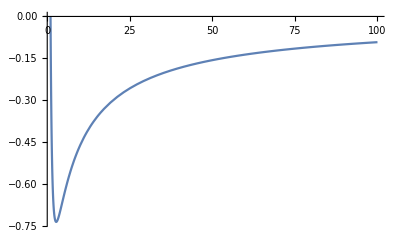

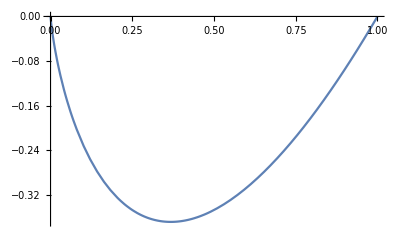

```mathematica
Plot[Log[1/x^2]/x,{x, 1, 100}]
Plot[x Log[x], {x, 0, 1}]
```

```mathematica
Clear["Global`*"];
Simplify[Solve[phi sigma^2+ px[(1-wx)/r] (sigma^2 ((-1+wx) (-1+wx) Pi/2+(-1+wx) (-1+wx) Pi/2+(-1+wx) wy Log[1-2 wx+wx^2]+(wy-wx wy) Log[r^2]))/(r wy)==1, wy]]
```

{{wy→(π sigma^2 (-1+wx)^2 px[(1-wx)/r])/(r-phi r sigma^2+sigma^2 (-1+wx) (Log[r^2]-Log[(-1+wx)^2]) px[(1-wx)/r])}}

```mathematica
Clear["Global`*"];
Expand[(r x - 1 + wx)^2+wy^2]
```

1-2 wx+wx^2+wy^2-2 r x+2 r wx x+r^2 x^2

```mathematica
D[1-2 wx+wx^2+wy^2-2 r x+2 r wx x+r^2 x^2, x]
```

-2 r+2 r wx+2 r^2 x

```mathematica
Clear["Global`*"];
Integrate[Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0],{myx,0,1}]
```

(√q0 sigma (-Erf[(-1+1/r)/(√2 √q0 sigma)]+Erf[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2))

```mathematica
Clear["Global`*"];
FullSimplify[x^2/((x-(1-wx)/r)^2+wy^2/r^2)-1]
```

-1+(r^2 x^2)/(wy^2+(-1+wx+r x)^2)

```mathematica
Clear["Global`*"];
sigma^2Integrate[2 (1-wx)(r x -1 + wx)/((r x - 1 + wx)^2 +wy^2),{x,0,1}]
```

ConditionalExpression[-(sigma^2 (-1+wx) (-Log[1-2 wx+wx^2+wy^2]+Log[1+r^2+2 r (-1+wx)-2 wx+wx^2+wy^2]))/r, ]

```mathematica
sigma^2Integrate[((1-wx)^2-wy^2)/((r x - 1 + wx)^2 +wy^2),{x,0,1}]
```

ConditionalExpression[(sigma^2 (1-2 wx+wx^2-wy^2) (-ArcTan[(-1+wx)/wy]+ArcTan[(-1+r+wx)/wy]))/(r wy), ]